```mathematica
Exit[]
```

```mathematica
LaunchKernels[16];
ParallelEvaluate[
Off[General::munfl];Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];
Off[NIntegrate::precw];Off[NIntegrate::inumr];Off[NIntegrate::eincr]];
Off[General::munfl];
Off[NIntegrate::slwcon];
Off[NIntegrate::ncvb];
Off[NIntegrate::precw];Off[NIntegrate::inumr];Off[NIntegrate::eincr];
```

## Setup the space

```mathematica
e[nuk1_,ndk1_,nuk2_,ndk2_,nuk3_,ndk3_,nuk4_,ndk4_]:=Flatten[TensorProduct@@(UnitVector/@({nuk1,ndk1,nuk2,ndk2,nuk3,ndk3,nuk4,ndk4}+1))];
cu1k=Sum[(-1)^(0)*KroneckerProduct[e[0,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4],e[1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4]],{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd1k=Sum[(-1)^(tuk1)*KroneckerProduct[e[tuk1,0,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4],e[tuk1,1,tuk2,tdk2,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu2k=Sum[(-1)^(tuk1+tdk1)*KroneckerProduct[e[tuk1,tdk1,0,tdk2,tuk3,tdk3,tuk4,tdk4],e[tuk1,tdk1,1,tdk2,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd2k=Sum[(-1)^(tuk1+tdk1+tuk2)*KroneckerProduct[e[tuk1,tdk1,tuk2,0,tuk3,tdk3,tuk4,tdk4],e[tuk1,tdk1,tuk2,1,tuk3,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu3k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,0,tdk3,tuk4,tdk4],e[tuk1,tdk1,tuk2,tdk2,1,tdk3,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tdk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cd3k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,0,tuk4,tdk4],e[tuk1,tdk1,tuk2,tdk2,tuk3,1,tuk4,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tuk4,0,1},{tdk4,0,1}];
cu4k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3+tdk3)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,0,tdk4],e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,1,tdk4]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tdk4,0,1}];
cd4k=Sum[(-1)^(tuk1+tdk1+tuk2+tdk2+tuk3+tdk3+tuk4)*KroneckerProduct[e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,0],e[tuk1,tdk1,tuk2,tdk2,tuk3,tdk3,tuk4,1]],{tuk1,0,1},{tdk1,0,1},{tuk2,0,1},{tdk2,0,1},{tuk3,0,1},{tdk3,0,1},{tuk4,0,1}];

(*anihilation operators in Fock space*)
fermif[x_,T_]=1/(Exp[x/T]+1);
delta[x_,dd_]=dd/(Pi(x^2+dd^2));cs={cu1k,cu2k,cu3k,cu4k,cd1k,cd2k,cd3k,cd4k};csall=Sum[cs[[i]],{i,1,4}];
```

## Setup the Hamiltonian and green function

```mathematica
hamiltonian[kx_,μ_,t_,tp_,U_]:=-t Exp[-I*kx](cu1k†.cu2k+cu2k†.cu3k+cu3k†.cu4k+cu4k†.cu1k+cd1k†.cd2k+cd2k†.cd3k+cd3k†.cd4k+cd4k†.cd1k)-t Exp[I*kx](cu2k†.cu1k+cu3k†.cu2k+cu4k†.cu3k+cu1k†.cu4k+cd2k†.cd1k+cd3k†.cd2k+cd4k†.cd3k+cd1k†.cd4k)+U(cu1k†.cu1k.cd1k†.cd1k+cu2k†.cu2k.cd2k†.cd2k+cu3k†.cu3k.cd3k†.cd3k+cu4k†.cu4k.cd4k†.cd4k)-μ(cu1k†.cu1k+cu2k†.cu2k+cu3k†.cu3k+cu4k†.cu4k+cd1k†.cd1k+cd2k†.cd2k+cd3k†.cd3k+cd4k†.cd4k);
green[kx_,μ_,t_,tp_,U_,β_,ω_,d_]:=With[{tt=Eigensystem[hamiltonian[kx,μ,t,tp,U]//N]},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,256}];
Sum[tvecs[[n]]†.csall.tvecs[[m]]*tvecs[[m]]†.csall†.tvecs[[n]]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/(ω+tvals[[n]]-tvals[[m]]-I*d),{n,256},{m,256}]/Z0/4
];(*greengr[kx_,μ_,t_,tp_,U_,β_,ω_,d_,bar1_,bar2_]:=With[{tt=SortBy[Eigensystem[hamiltonian[kx,μ,t,tp,U]//N]ᵀ,First]ᵀ},
tvals=tt[[1]];
tvecs=tt[[2]];
Z0=Sum[Exp[-β*tvals[[i]]],{i,bar2}];
Sum[tvecs[[n]]†.csall.tvecs[[m]]*tvecs[[m]]†.csall†.tvecs[[n]]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/(ω+tvals[[n]]-tvals[[m]]-I*d),{n,1,bar1},{m,1,bar2}]/Z0/4+Sum[tvecs[[n]]†.csall.tvecs[[m]]*tvecs[[m]]†.csall†.tvecs[[n]]*(Exp[-β*tvals[[n]]]+Exp[-β*tvals[[m]]])/(ω+tvals[[n]]-tvals[[m]]-I*d),{n,bar1+1,bar2},{m,1,bar1}]/Z0/4
];*)
```

```mathematica
Eigensystem[hamiltonian[kx,μ,t,tp,U]//N]
```

```mathematica
tt=SortBy[Eigensystem[hamiltonian[0Pi/40+0.00001,4,1,0,8]//N]ᵀ,First]ᵀ
```

```mathematica
tt[[1]]+4*4
```

{-1.32023,-0.987918,-0.987918,-0.987918,-0.513676,-0.472136,-0.472136,-0.472136,-0.472136,-0.472136,-0.472136,-2.13163×10^-14,-7.10543×10^-15,1.77636×10^-15,3.55271×10^-15,1.77636×10^-14,1.67543,1.67543,1.67543,1.67543,1.67546,1.67546,1.67546,1.67546,2.,2.,2.,2.,2.,2.,2.,2.,2.70848,2.70848,2.70848,2.70848,2.70852,2.70852,2.70852,2.70852,3.99998,3.99998,3.99998,3.99998,3.99998,3.99998,3.99998,3.99998,4.00002,4.00002,4.00002,4.00002,4.00002,4.00002,4.00002,4.00002,4.53589,4.53589,4.53589,4.53589,4.53591,4.53591,4.53591,4.53591,4.79225,4.79225,4.79225,5.17157,5.17157,5.17157,5.17157,5.17158,5.17158,5.17158,5.17158,5.78017,5.78017,5.78017,5.99998,5.99998,5.99998,5.99998,5.99998,5.99998,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.,6.00002,6.00002,6.00002,6.00002,6.00002,6.00002,7.19344,7.52786,7.52786,7.52786,7.52786,7.52787,7.52787,7.99997,7.99997,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.,8.00003,8.00003,8.47214,8.47214,8.47214,8.47214,8.47214,8.47214,8.80656,9.99998,9.99998,9.99998,9.99998,9.99998,9.99998,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.,10.2198,10.2198,10.2198,10.8284,10.8284,10.8284,10.8284,10.8284,10.8284,10.8284,10.8284,11.2078,11.2078,11.2078,11.4641,11.4641,11.4641,11.4641,11.4641,11.4641,11.4641,11.4641,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,12.,13.2915,13.2915,13.2915,13.2915,13.2915,13.2915,13.2915,13.2915,14.,14.,14.,14.,14.,14.,14.,14.,14.3245,14.3245,14.3245,14.3245,14.3246,14.3246,14.3246,14.3246,16.,16.,16.,16.,16.,16.4721,16.4721,16.4721,16.4721,16.4721,16.4721,16.5137,16.9879,16.9879,16.9879,17.3202}

## Calculate the green function at U = 0

```mathematica
Nk = 100;
dw = 0.1;
wmax = 8;
Nw = 2*(wmax/dw)+1;
wList=Range[-wmax,wmax,dw];
dk =2* Pi/Nk;
kList = Range[0,2*Pi,dk];
t=1;
U=0;
μ = U/2;
β=10000;
η=0.2;
tp=0;
GF=ParallelTable[green[kList[[i]],μ,t,tp,U,β,wList,η],{i,1,Nk+1}];
```

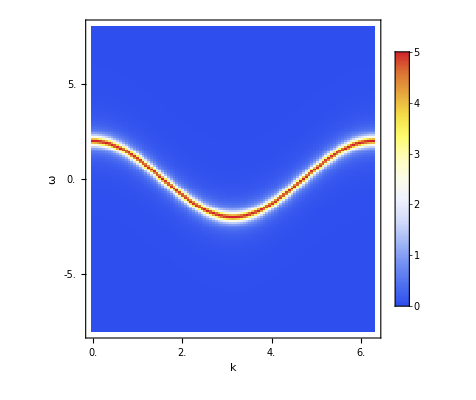

```mathematica
Heat=ArrayPlot[Transpose[Im[GF]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"times New Roman"},FrameTicks->{Automatic,Automatic,None}]
```

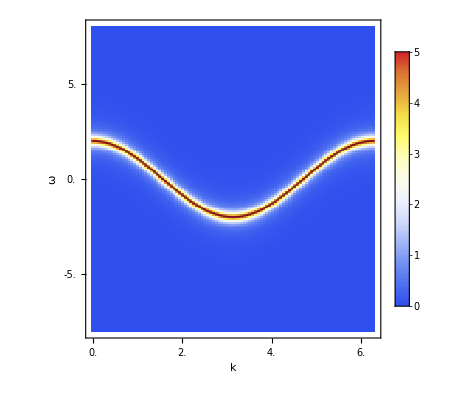

```mathematica
pZero=ListContourPlot[Reverse[Transpose[Re[GF]]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,Frame->False,Axes->False,PlotRange->All,MaxPlotPoints->200];

Show[Heat,pZero,PlotRange->All,ImagePadding->All]
```

## Calculate the green function at U = 8

```mathematica
Nk = 100;
dw = 0.1;
wmax = 8;
Nw = 2*(wmax/dw)+1;
wList=Range[-wmax,wmax,dw];
dk =2* Pi/Nk;
kList = Range[0,2*Pi,dk];
t=1;
U=8;
μ = U/2;
β=10000;
η=0.2;
tp=0;
GFU8=ParallelTable[green[kList[[i]],μ,t,tp,U,β,wList,η],{i,1,Nk+1}];
```

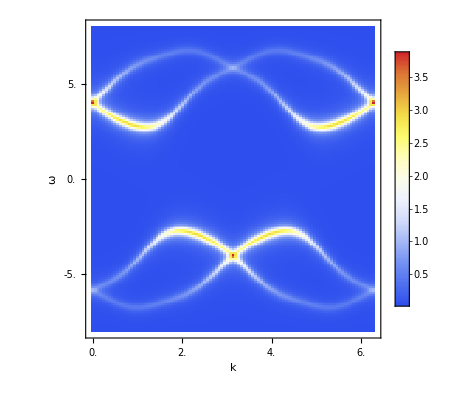

```mathematica
pHeatspec=ArrayPlot[Transpose[Im[GFU8]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"times New Roman"},FrameTicks->{Automatic,Automatic,None}]
```

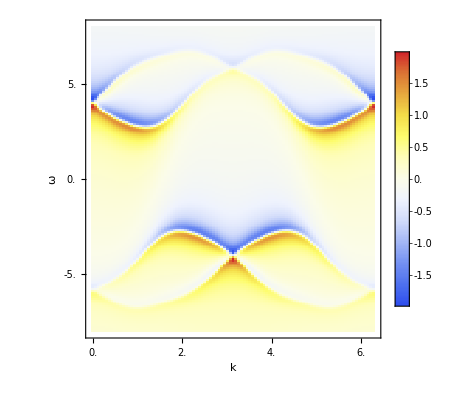

```mathematica
ArrayPlot[Transpose[Re[GFU8]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"times New Roman"},FrameTicks->{Automatic,Automatic,None}]
```

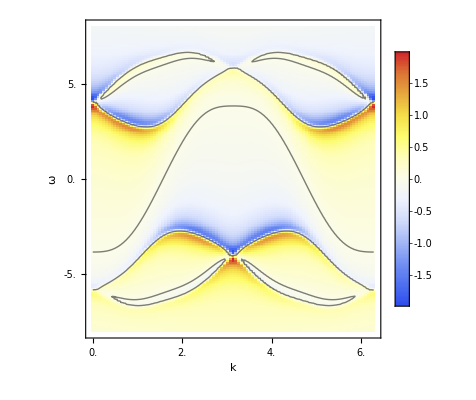

```mathematica
(*assume:ReGF=Re[GFU8];(*dims:{Nk,Nw} with indices {k-index,w-index}*)kList (length Nk),wList (length Nw)*)ReGF=Re[GFU8];

(*If your ArrayPlot uses Transpose[ReGF],that means:x-axis is ω (wList),y-axis is k (kList) and data index ordering should match that mapping.*)

f=ListInterpolation[Transpose[ReGF],{{Min[wList],Max[wList]},{Min[kList],Max[kList]}},InterpolationOrder->1];

preGHeat=ArrayPlot[Transpose[ReGF],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"Times New Roman"},Axes->True,FrameTicks->{Automatic,Automatic,None}];

pZero=ListContourPlot[Reverse[Transpose[ReGF]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},Contours->{0},ContourStyle->{Thick,Black},ContourShading->None,Frame->False,Axes->False,PlotRange->All,MaxPlotPoints->200];

Show[preGHeat,pZero,PlotRange->All,ImagePadding->All]
```

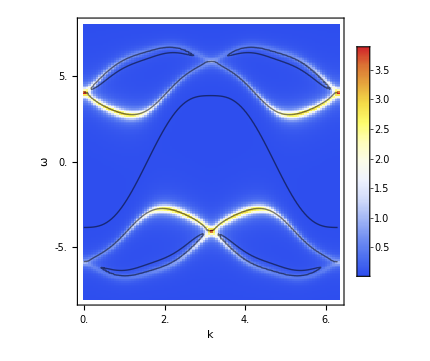

```mathematica
Show[pHeatspec,pZero,PlotRange->All,ImagePadding->All]
```

## Calculate the self energy at U = 8

```mathematica
Sigma = 1/GFU8-1/GF;
```

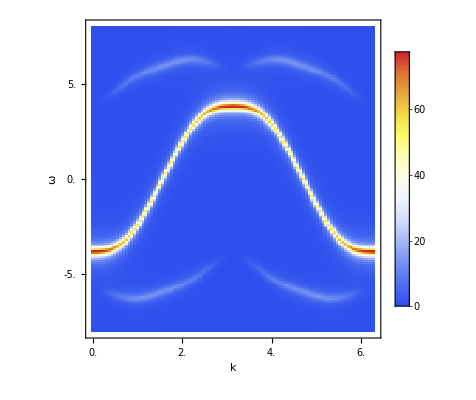

```mathematica
ArrayPlot[Transpose[-Im[Sigma]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"times New Roman"},FrameTicks->{Automatic,Automatic,None}]
```

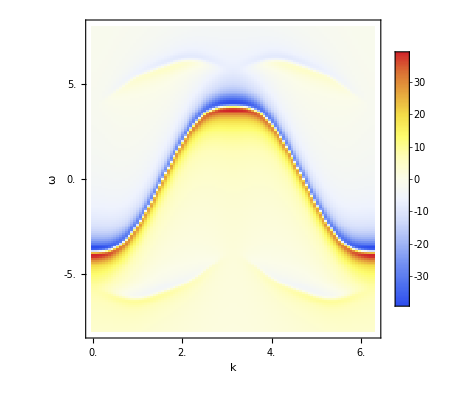

```mathematica
ArrayPlot[-Transpose[Re[Sigma]],DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},ColorFunction->ColorData["TemperatureMap"],ColorFunctionScaling->True,ColorFunctionScaling->True,Frame->True,FrameLabel->{"ω","k"},PlotLegends->Automatic,AspectRatio->1,BaseStyle->{FontSize->20,FontFamily->"times New Roman"},FrameTicks->{Automatic,Automatic,None}]
```

```mathematica
ClearAll[ZeroContourStyled];
Options[ZeroContourStyled]={"Threshold"->0.1,"InterpolationOrder"->1,"MaxPlotPoints"->200,"MaxRecursion"->2,"ReverseY"->True,(*与你现在 Reverse[Transpose[ReGF]] 一致*)"StyleSolid"->{Thick,Black},"StyleDashed"->{Thick,Dashed,Black}};

ZeroContourStyled[ReGF_,ImGF_,kList_,wList_,opts:OptionsPattern[]]:=Module[{thresh,iord,mpp,mrec,reverseY,styleSolid,styleDashed,imf,reData,contourGraphics,lines,splitByIm,solidLines={},dashedLines={},parts},thresh=OptionValue["Threshold"];
iord=OptionValue["InterpolationOrder"];
mpp=OptionValue["MaxPlotPoints"];
mrec=OptionValue["MaxRecursion"];
reverseY=OptionValue["ReverseY"];
styleSolid=OptionValue["StyleSolid"];
styleDashed=OptionValue["StyleDashed"];
(*插值函数：给定 (k,ω)->Im 值*)imf=ListInterpolation[Transpose[ImGF],{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},InterpolationOrder->iord];
(*用于 contour 的 Re 数据（按需翻转 y）*)reData=If[TrueQ[reverseY],Reverse[Transpose[ReGF]],Transpose[ReGF]];
contourGraphics=Normal@ListContourPlot[reData,DataRange->{{Min[kList],Max[kList]},{Min[wList],Max[wList]}},Contours->{0},ContourShading->None,Frame->False,Axes->False,PlotRange->All,MaxPlotPoints->mpp];
lines=Cases[contourGraphics,Line[pts_]:>pts,Infinity];
splitByIm[line_]:=Module[{vals,groups,solids,dashed},vals=imf@@@line;(*Im(k,ω) 沿 contour*)groups=SplitBy[Transpose[{line,vals}],#[[2]]>thresh&];
solids=Line[#[[All,1]]]&/@Select[groups,#[[1,2]]>thresh&];
dashed=Line[#[[All,1]]]&/@Select[groups,#[[1,2]]<=thresh&];
{solids,dashed}];
parts=splitByIm/@lines;
solidLines=Flatten[parts[[All,1]],1];
dashedLines=Flatten[parts[[All,2]],1];
Graphics[{Sequence@@styleSolid,solidLines(*,Sequence@@styleDashed,dashedLines*)}]];
```

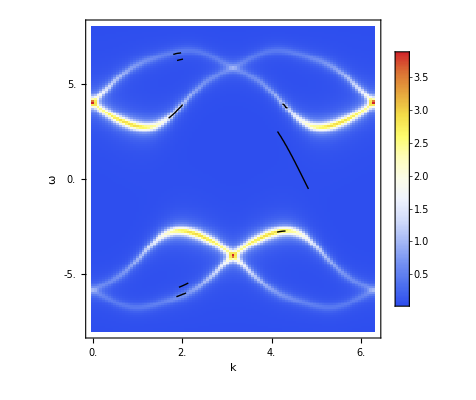

```mathematica
pZeroStyled=ZeroContourStyled[ReGF,Im[GFU8],kList,wList,"Threshold"->1,"MaxPlotPoints"->200];

Show[pHeatspec,pZeroStyled,PlotRange->All,ImagePadding->All]
```